```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
SeedRandom[1];
<<"Sampler4`";
SIGMA=Table[0,10,10];
For[i=1,i≤10,i++,SIGMA[[i,i]]=1/24^(i-1)];
U[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=N[1/2 Simplify[{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}.LinearSolve[SIGMA,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}]]];
dU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=GradientG[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
ddU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=HessianH[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
dddU[x1_,x2_,x3_,x4_,x5_,x6_,x7_,x8_,x9_,x10_]=D3[U[x1,x2,x3,x4,x5,x6,x7,x8,x9,x10],{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10}];
```

```mathematica
Dim=10;
CHAINS=3;
STEPS=3;
dKdq[p_,q_]=0;
QS=hmc[Dim,5000,10000,{}];
```

1001238832.3.722850.7931150.35833513.1299{1,4}{1,4}0.000581829262729.0.000581829TrueFalse

20024.51545×10^73.917640.6299190.3344629.82876{1,4}{1,4}0.00003031254.51546×10^70.0000303125FalseFalse

30037.64418×10^101.055220.5709790.42931711.9386{1,2,3}{1,4}5.53514×10^-77.64418×10^105.53514×10^-7FalseFalse

40044.18624×10^122.519860.5721940.41533718.6612{1,2}{4}9.0504×10^-84.18624×10^129.0504×10^-8FalseFalse

50054.98923×10^132.166170.7640690.40864418.5604{1,2}{4}2.62158×10^-84.98923×10^132.62158×10^-8FalseFalse

60064.98923×10^130.4743470.4322960.51233519.1612{1,2}{4}2.62158×10^-84.98923×10^132.62158×10^-8FalseFalse

70074.98923×10^130.9203690.5286210.451168.01992{1,2}{4}2.62158×10^-84.98923×10^132.62158×10^-8FalseFalse

80084.98923×10^131.981660.4658950.46254811.9192{1,2}{4}2.62158×10^-84.98923×10^132.62158×10^-8FalseFalse

90094.98923×10^130.7417430.7409110.44875417.5945{1,2}{4}2.62158×10^-84.98923×10^132.62158×10^-8FalseFalse

{1.,0.0416667,0.00173611,0.000072338,3.01408×10^-6,1.25587×10^-7,5.23278×10^-9,2.18033×10^-10,9.08469×10^-12,3.78529×10^-13}

{0.95117,0.0425101,0.0016611,0.0000730234,3.20775×10^-6,1.20654×10^-7,4.79706×10^-9,2.15542×10^-10,8.92838×10^-12,3.56809×10^-13}

{0.97528,1.01007,0.978158,1.00473,1.03163,0.980166,0.957461,0.994272,0.99136,0.970886}

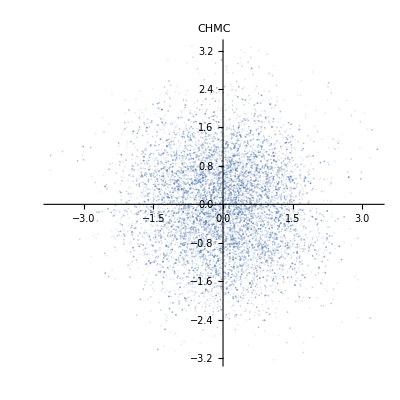

```mathematica
Table[1/24^(i-1),{i,1,10}]//N
Diagonal[Covariance[QS]]

QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[QS1[[;;,{1,10}]],PlotLabel->CHMC,PlotStyle->Opacity[.2],AspectRatio->1]
```